```mathematica
eq1= lambda*x + 1/2 - z;
eq2=x^2 + y^2 - z^2;
sol[lambda_]={y,z}/.Solve[{eq1==0, eq2==0}, {y,z}]
```

{{-1/2 √(1+4 lambda x-4 x^2+4 lambda^2 x^2),1/2 (1+2 lambda x)},{1/2 √(1+4 lambda x-4 x^2+4 lambda^2 x^2),1/2 (1+2 lambda x)}}

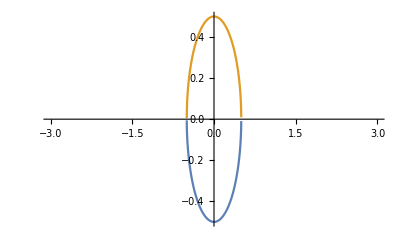

```mathematica
grafico1=Plot[ {sol[0][[1,1]], sol[0][[2,1]] },{x,-3,3}]
```

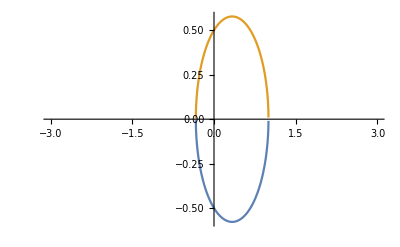

```mathematica
grafico2=Plot[{sol[0.5][[1,1]], sol[0.5][[2,1]]},{x,-3,3}]
```

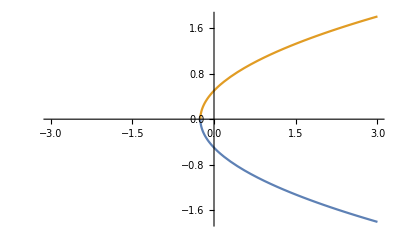

```mathematica
grafico3=Plot[{sol[1][[1,1]],sol[1][[2,1]]},{x,-3,3}]
```

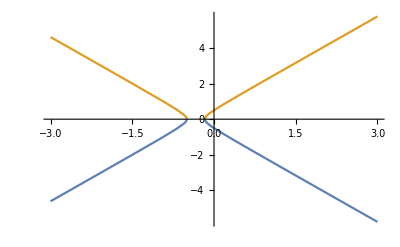

```mathematica
grafico4=Plot[{sol[2][[1,1]], sol[2][[2,1]]},{x,-3,3}]
```

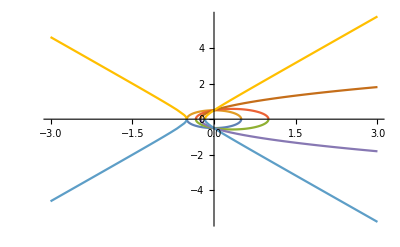

```mathematica
graficotot=Plot[{ sol[0][[1,1]], sol[0][[2,1]]  , sol[0.5][[1,1]], sol[0.5][[2,1]] , sol[1][[1,1]],sol[1][[2,1]] , sol[2][[1,1]], sol[2][[2,1]] } , {x,-3,3}]
```

```mathematica
sup1[lambda_]=1/2 + lambda*x ;
sup2=Sqrt[x^2 + y^2 ];
Manipulate[Plot3D[ {sup1[lambda],sup2}, {x,-3,3},{y,-3,3}] , {lambda,-10,10}]
```